```mathematica
Manipulate[ 
Plot[ChebyshevT[n, z0 x], {x, -r, r}, AxesLabel -> { "x", Row[{"T_n(z_0x) = ", TraditionalForm[ChebyshevT[n, z0 x]]}]
}
, PlotRange -> {{-r, r}, {-r, r}}
, Epilog -> {
(*Color -> Red,*)
PointSize -> Large,
Point[{1, ChebyshevT[n, z0 ]}],
Point[{-1, ChebyshevT[n, -z0 ]}]
}
],
{n, 1, 10, 1, Appearance->"Labeled"},
{{z0, 1, "z_0"}, 1, 5, Appearance->"Labeled"},
{{r, 1, "scale"}, 1, 10, Appearance->"Labeled"} ]
```

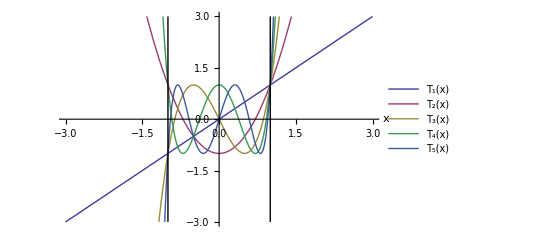

```mathematica
p = With[{r = 3, z0 = 1, n = 5},
Plot[ChebyshevT[#, z0 x]& /@ Range[n] // Evaluate, {x, -r, r}, AxesLabel -> { "x"(*, "T_n(x)"*) } 
, PlotRange -> {{-r, r}, {-r, r}}
, Epilog -> {
Line[{{1,-r}, {1, r}}],
Line[{{-1,-r}, {-1, r}}]
}
, PlotLegends->Placed[ Row[{HoldForm[TraditionalForm[ChebyshevT[#, x] ]]
(*, " = ", TraditionalForm[ChebyshevT[#, x] ]*)
} ] &/@ Range[n], {Right,Bottom} ]
]]
```

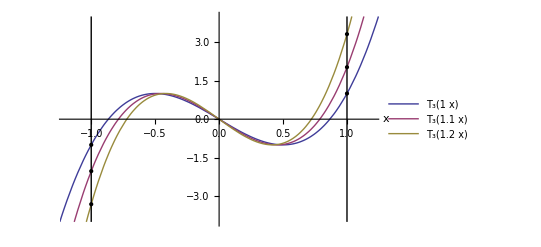

```mathematica
q = With[{r = 4, n = 3, z0 = {1,1.1, 1.2}},
Plot[ChebyshevT[n, # x]& /@z0 // Evaluate, {x, -r, r}, AxesLabel -> { "x"(*, "T_n(x)"*) } 
, PlotRange -> {{-1.2, 1.2}, {-r, r}}
, Epilog -> {
Flatten[{
Line[{{1,-r}, {1, r}}],
Line[{{-1,-r}, {-1, r}}],
PointSize -> Medium,
Point[{1, ChebyshevT[n, # ]}] &/@ z0,
Point[{-1, ChebyshevT[n, -# ]}] &/@ z0
}
]
}
, PlotLegends->Placed[ Row[{HoldForm[TraditionalForm[ChebyshevT[n, #x] ]]
(*, " = ", TraditionalForm[ChebyshevT[#, x] ]*)
} ] &/@z0, {Right,Bottom} ]
]]
```

```mathematica
<<peeters` ;
(*peeters`setGitDir[ "notes\\blogit" ] *)
peeters`setGitDir[ "figures\\ece1229" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229

```mathematica
peeters`exportForLatex["ChebyChevOneToFiveFig1", p]
peeters`exportForLatex["ChebyChevThreeScaledFig2", q]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/ChebyChevOneToFiveFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/ChebyChevOneToFiveFig1pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/ChebyChevThreeScaledFig2.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/ChebyChevThreeScaledFig2pn.png}